#### Compuertas consecutivas en circuito de un solo qubit

```mathematica
gates210=createCircuit[2,10][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
gates310=createCircuit[3,10][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
gates410=createCircuit[4,10][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
gates250=createCircuit[2,50][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
gates350=createCircuit[3,50][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
gates450=createCircuit[4,50][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
gates2100=createCircuit[2,100][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
gates3100=createCircuit[3,100][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
gates4100=createCircuit[4,100][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

```mathematica
--------------------------------------------------------------------------------------------------------------------------
```

```mathematica
gates210["globalAbsError"]
gates210["globalRelError"]
```

1.61953

1.14518

```mathematica
Print["Hadamard 2 vértices 10 evaluaciones"]
graphGateCycle[gates210][1][[1]]
graphGateCycle[gates210][1][[2]]
graphGateCycle[gates210][1][[3]]
Print["S 2 vértices 10 evaluaciones"]
graphGateCycle[gates210][2][[1]]
graphGateCycle[gates210][2][[2]]
graphGateCycle[gates210][2][[3]]
Print["T 2 vértices 10 evaluaciones"]
graphGateCycle[gates210][3][[1]]
graphGateCycle[gates210][3][[2]]
graphGateCycle[gates210][3][[3]]
Print["PauliX 2 vértices 10 evaluaciones"]
graphGateCycle[gates210][4][[1]]
graphGateCycle[gates210][4][[2]]
graphGateCycle[gates210][4][[3]]
Print["PauliY 2 vértices 10 evaluaciones"]
graphGateCycle[gates210][5][[1]]
graphGateCycle[gates210][5][[2]]
graphGateCycle[gates210][5][[3]]
Print["PauliZ 2 vértices 10 evaluaciones"]
graphGateCycle[gates210][6][[1]]
graphGateCycle[gates210][6][[2]]
graphGateCycle[gates210][6][[3]]
Print["RootNOT 2 vértices 10 evaluaciones"]
graphGateCycle[gates210][7][[1]]
graphGateCycle[gates210][7][[2]]
graphGateCycle[gates210][7][[3]]
```

```mathematica
------------------------------------------
```

```mathematica
gates250["globalAbsError"]
gates250["globalRelError"]
```

1.90174

1.34473

```mathematica
Print["Hadamard 2 vértices 50 evaluaciones"]
graphGateCycle[gates250][1][[1]]
graphGateCycle[gates250][1][[2]]
graphGateCycle[gates250][1][[3]]
Print["S 2 vértices 50 evaluaciones"]
graphGateCycle[gates250][2][[1]]
graphGateCycle[gates250][2][[2]]
graphGateCycle[gates250][2][[3]]
Print["T 2 vértices 50 evaluaciones"]
graphGateCycle[gates250][3][[1]]
graphGateCycle[gates250][3][[2]]
graphGateCycle[gates250][3][[3]]
Print["PauliX 2 vértices 50 evaluaciones"]
graphGateCycle[gates250][4][[1]]
graphGateCycle[gates250][4][[2]]
graphGateCycle[gates250][4][[3]]
Print["PauliY 2 vértices 50 evaluaciones"]
graphGateCycle[gates250][5][[1]]
graphGateCycle[gates250][5][[2]]
graphGateCycle[gates250][5][[3]]
Print["PauliZ 2 vértices 50 evaluaciones"]
graphGateCycle[gates250][6][[1]]
graphGateCycle[gates250][6][[2]]
graphGateCycle[gates250][6][[3]]
Print["RootNOT 2 vértices 50 evaluaciones"]
graphGateCycle[gates250][7][[1]]
graphGateCycle[gates250][7][[2]]
graphGateCycle[gates250][7][[3]]
```

```mathematica
---------------------------------------------------
```

```mathematica
gates2100["globalAbsError"]
gates2100["globalRelError"]
```

1.68859

1.19401

```mathematica
Print["Hadamard 2 vértices 100 evaluaciones"]
graphGateCycle[gates2100][1][[1]]
graphGateCycle[gates2100][1][[2]]
graphGateCycle[gates2100][1][[3]]
Print["S 2 vértices 100 evaluaciones"]
graphGateCycle[gates2100][2][[1]]
graphGateCycle[gates2100][2][[2]]
graphGateCycle[gates2100][2][[3]]
Print["T 2 vértices 100 evaluaciones"]
graphGateCycle[gates2100][3][[1]]
graphGateCycle[gates2100][3][[2]]
graphGateCycle[gates2100][3][[3]]
Print["PauliX 2 vértices 100 evaluaciones"]
graphGateCycle[gates2100][4][[1]]
graphGateCycle[gates2100][4][[2]]
graphGateCycle[gates2100][4][[3]]
Print["PauliY 2 vértices 100 evaluaciones"]
graphGateCycle[gates2100][5][[1]]
graphGateCycle[gates2100][5][[2]]
graphGateCycle[gates2100][5][[3]]
Print["PauliZ 2 vértices 100 evaluaciones"]
graphGateCycle[gates2100][6][[1]]
graphGateCycle[gates2100][6][[2]]
graphGateCycle[gates2100][6][[3]]
Print["RootNOT 2 vértices 100 evaluaciones"]
graphGateCycle[gates2100][7][[1]]
graphGateCycle[gates2100][7][[2]]
graphGateCycle[gates2100][7][[3]]
```

```mathematica
--------------------------------------------------------------------------
```

```mathematica
gates310["globalAbsError"]
gates310["globalRelError"]
```

0.163661

0.115726

```mathematica
Print["Hadamard 3 vértices 10 evaluaciones"]
graphGateCycle[gates310][1][[1]]
graphGateCycle[gates310][1][[2]]
graphGateCycle[gates310][1][[3]]
Print["S 3 vértices 10 evaluaciones"]
graphGateCycle[gates310][2][[1]]
graphGateCycle[gates310][2][[2]]
graphGateCycle[gates310][2][[3]]
Print["T 3 vértices 10 evaluaciones"]
graphGateCycle[gates310][3][[1]]
graphGateCycle[gates310][3][[2]]
graphGateCycle[gates310][3][[3]]
Print["PauliX 3 vértices 10 evaluaciones"]
graphGateCycle[gates310][4][[1]]
graphGateCycle[gates310][4][[2]]
graphGateCycle[gates310][4][[3]]
Print["PauliY 3 vértices 10 evaluaciones"]
graphGateCycle[gates310][5][[1]]
graphGateCycle[gates310][5][[2]]
graphGateCycle[gates310][5][[3]]
Print["PauliZ 3 vértices 10 evaluaciones"]
graphGateCycle[gates310][6][[1]]
graphGateCycle[gates310][6][[2]]
graphGateCycle[gates310][6][[3]]
Print["RootNOT 3 vértices 10 evaluaciones"]
graphGateCycle[gates310][7][[1]]
graphGateCycle[gates310][7][[2]]
graphGateCycle[gates310][7][[3]]
```

```mathematica
------------------------------------------------
```

```mathematica
gates350["globalAbsError"]
gates350["globalRelError"]
```

1.00388×10^-6

7.09853×10^-7

```mathematica
Print["Hadamard 3 vértices 50 evaluaciones"]
graphGateCycle[gates350][1][[1]]
graphGateCycle[gates350][1][[2]]
graphGateCycle[gates350][1][[3]]
Print["S 3 vértices 50 evaluaciones"]
graphGateCycle[gates350][2][[1]]
graphGateCycle[gates350][2][[2]]
graphGateCycle[gates350][2][[3]]
Print["T 3 vértices 50 evaluaciones"]
graphGateCycle[gates350][3][[1]]
graphGateCycle[gates350][3][[2]]
graphGateCycle[gates350][3][[3]]
Print["PauliX 3 vértices 50 evaluaciones"]
graphGateCycle[gates350][4][[1]]
graphGateCycle[gates350][4][[2]]
graphGateCycle[gates350][4][[3]]
Print["PauliY 3 vértices 50 evaluaciones"]
graphGateCycle[gates350][5][[1]]
graphGateCycle[gates350][5][[2]]
graphGateCycle[gates350][5][[3]]
Print["PauliZ 3 vértices 50 evaluaciones"]
graphGateCycle[gates350][6][[1]]
graphGateCycle[gates350][6][[2]]
graphGateCycle[gates350][6][[3]]
Print["RootNOT 3 vértices 50 evaluaciones"]
graphGateCycle[gates350][7][[1]]
graphGateCycle[gates350][7][[2]]
graphGateCycle[gates350][7][[3]]
```

```mathematica
--------------------------------------------
```

```mathematica
gates3100["globalAbsError"]
gates3100["globalRelError"]
```

0.494757

0.349846

```mathematica
Print["Hadamard 3 vértices 100 evaluaciones"]
graphGateCycle[gates3100][1][[1]]
graphGateCycle[gates3100][1][[2]]
graphGateCycle[gates3100][1][[3]]
Print["S 3 vértices 100 evaluaciones"]
graphGateCycle[gates3100][2][[1]]
graphGateCycle[gates3100][2][[2]]
graphGateCycle[gates3100][2][[3]]
Print["T 3 vértices 100 evaluaciones"]
graphGateCycle[gates3100][3][[1]]
graphGateCycle[gates3100][3][[2]]
graphGateCycle[gates3100][3][[3]]
Print["PauliX 3 vértices 100 evaluaciones"]
graphGateCycle[gates3100][4][[1]]
graphGateCycle[gates3100][4][[2]]
graphGateCycle[gates3100][4][[3]]
Print["PauliY 3 vértices 100 evaluaciones"]
graphGateCycle[gates3100][5][[1]]
graphGateCycle[gates3100][5][[2]]
graphGateCycle[gates3100][5][[3]]
Print["PauliZ 3 vértices 100 evaluaciones"]
graphGateCycle[gates3100][6][[1]]
graphGateCycle[gates3100][6][[2]]
graphGateCycle[gates3100][6][[3]]
Print["RootNOT 3 vértices 100 evaluaciones"]
graphGateCycle[gates3100][7][[1]]
graphGateCycle[gates3100][7][[2]]
graphGateCycle[gates3100][7][[3]]
```

```mathematica
----------------------------------------------------------
```

```mathematica
gates410["globalAbsError"]
gates410["globalRelError"]
```

7.19765×10^-7

5.0895×10^-7

```mathematica
Print["Hadamard 4 vértices 10 evaluaciones"]
graphGateCycle[gates410][1][[1]]
graphGateCycle[gates410][1][[2]]
graphGateCycle[gates410][1][[3]]
Print["S 4 vértices 10 evaluaciones"]
graphGateCycle[gates410][2][[1]]
graphGateCycle[gates410][2][[2]]
graphGateCycle[gates410][2][[3]]
Print["T 4 vértices 10 evaluaciones"]
graphGateCycle[gates410][3][[1]]
graphGateCycle[gates410][3][[2]]
graphGateCycle[gates410][3][[3]]
Print["PauliX 4 vértices 10 evaluaciones"]
graphGateCycle[gates410][4][[1]]
graphGateCycle[gates410][4][[2]]
graphGateCycle[gates410][4][[3]]
Print["PauliY 4 vértices 10 evaluaciones"]
graphGateCycle[gates410][5][[1]]
graphGateCycle[gates410][5][[2]]
graphGateCycle[gates410][5][[3]]
Print["PauliZ 4 vértices 10 evaluaciones"]
graphGateCycle[gates410][6][[1]]
graphGateCycle[gates410][6][[2]]
graphGateCycle[gates410][6][[3]]
Print["RootNOT 4 vértices 10 evaluaciones"]
graphGateCycle[gates410][7][[1]]
graphGateCycle[gates410][7][[2]]
graphGateCycle[gates410][7][[3]]
```

```mathematica
----------------------------------------------
```

```mathematica
gates450["globalAbsError"]
gates450["globalRelError"]
```

1.15×10^-6

8.13176×10^-7

```mathematica
Print["Hadamard 4 vértices 50 evaluaciones"]
graphGateCycle[gates450][1][[1]]
graphGateCycle[gates450][1][[2]]
graphGateCycle[gates450][1][[3]]
Print["S 4 vértices 50 evaluaciones"]
graphGateCycle[gates450][2][[1]]
graphGateCycle[gates450][2][[2]]
graphGateCycle[gates450][2][[3]]
Print["T 4 vértices 50 evaluaciones"]
graphGateCycle[gates450][3][[1]]
graphGateCycle[gates450][3][[2]]
graphGateCycle[gates450][3][[3]]
Print["PauliX 4 vértices 50 evaluaciones"]
graphGateCycle[gates450][4][[1]]
graphGateCycle[gates450][4][[2]]
graphGateCycle[gates450][4][[3]]
Print["PauliY 4 vértices 50 evaluaciones"]
graphGateCycle[gates450][5][[1]]
graphGateCycle[gates450][5][[2]]
graphGateCycle[gates450][5][[3]]
Print["PauliZ 4 vértices 50 evaluaciones"]
graphGateCycle[gates450][6][[1]]
graphGateCycle[gates450][6][[2]]
graphGateCycle[gates450][6][[3]]
Print["RootNOT 4 vértices 50 evaluaciones"]
graphGateCycle[gates450][7][[1]]
graphGateCycle[gates450][7][[2]]
graphGateCycle[gates450][7][[3]]
```

```mathematica
------------------------------------------------
```

```mathematica
gates4100["globalAbsError"]
gates4100["globalRelError"]
```

1.52928×10^-6

1.08137×10^-6

Hadamard 4 vértices 100 evaluaciones

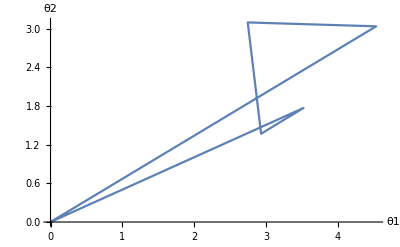

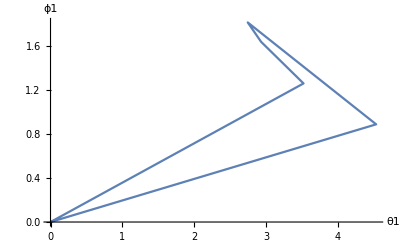

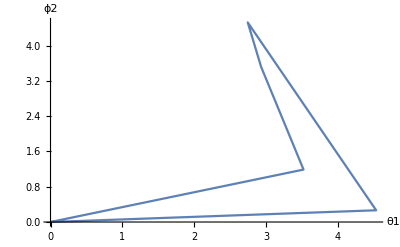

S 4 vértices 100 evaluaciones

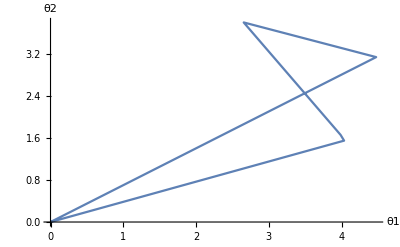

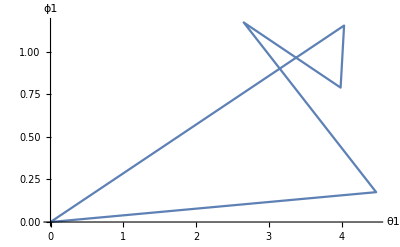

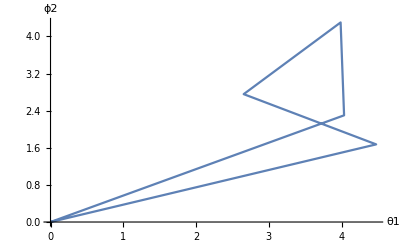

T 4 vértices 100 evaluaciones

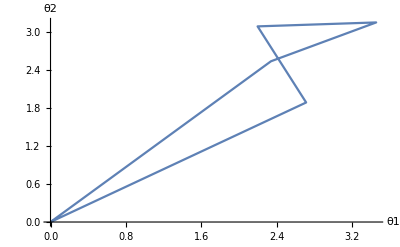

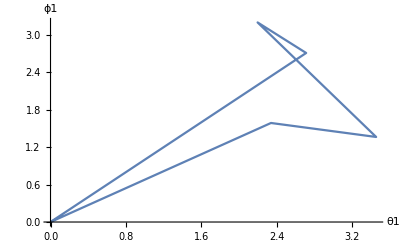

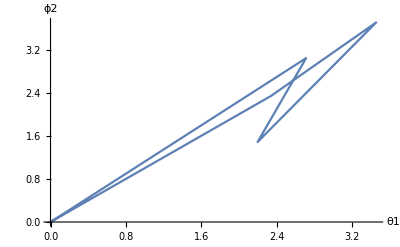

PauliX 4 vértices 100 evaluaciones

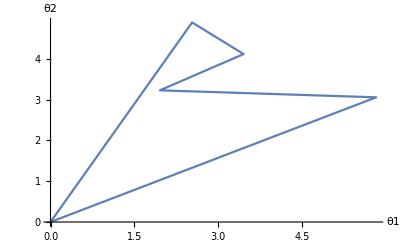

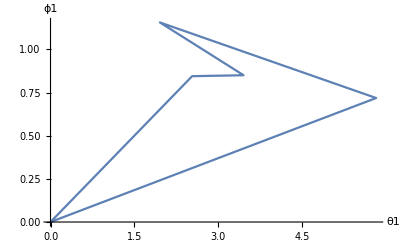

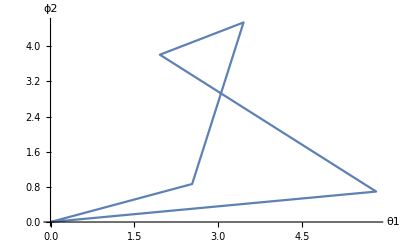

PauliY 4 vértices 100 evaluaciones

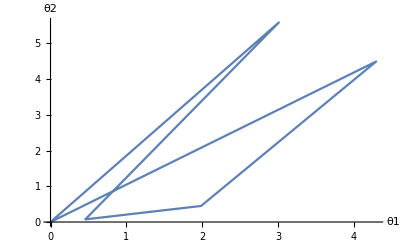

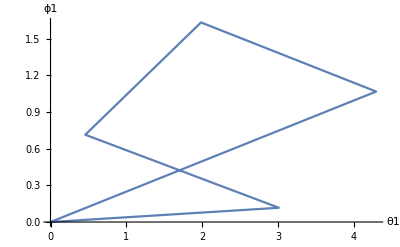

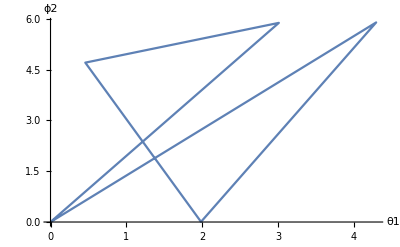

PauliZ 4 vértices 100 evaluaciones

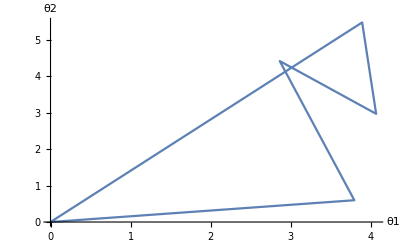

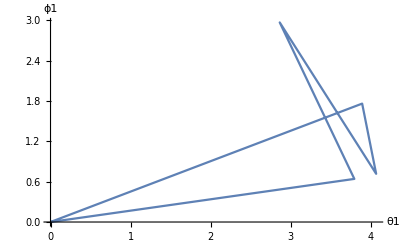

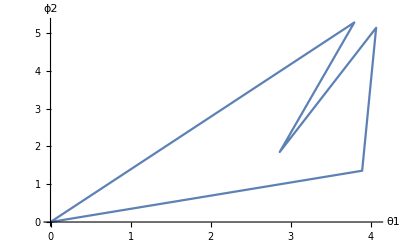

RootNOT 4 vértices 100 evaluaciones

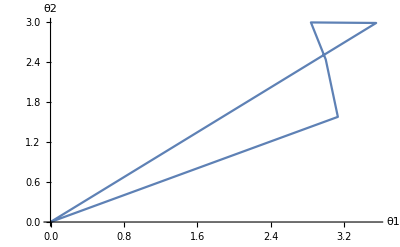

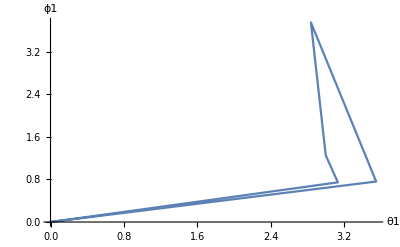

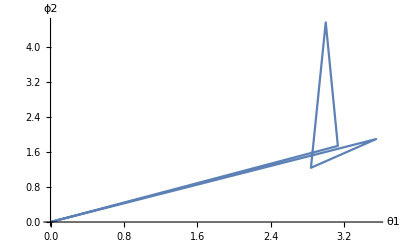

```mathematica
Print["Hadamard 4 vértices 100 evaluaciones"]
graphGateCycle[gates4100][1][[1]]
graphGateCycle[gates4100][1][[2]]
graphGateCycle[gates4100][1][[3]]
Print["S 4 vértices 100 evaluaciones"]
graphGateCycle[gates4100][2][[1]]
graphGateCycle[gates4100][2][[2]]
graphGateCycle[gates4100][2][[3]]
Print["T 4 vértices 100 evaluaciones"]
graphGateCycle[gates4100][3][[1]]
graphGateCycle[gates4100][3][[2]]
graphGateCycle[gates4100][3][[3]]
Print["PauliX 4 vértices 100 evaluaciones"]
graphGateCycle[gates4100][4][[1]]
graphGateCycle[gates4100][4][[2]]
graphGateCycle[gates4100][4][[3]]
Print["PauliY 4 vértices 100 evaluaciones"]
graphGateCycle[gates4100][5][[1]]
graphGateCycle[gates4100][5][[2]]
graphGateCycle[gates4100][5][[3]]
Print["PauliZ 4 vértices 100 evaluaciones"]
graphGateCycle[gates4100][6][[1]]
graphGateCycle[gates4100][6][[2]]
graphGateCycle[gates4100][6][[3]]
Print["RootNOT 4 vértices 100 evaluaciones"]
graphGateCycle[gates4100][7][[1]]
graphGateCycle[gates4100][7][[2]]
graphGateCycle[gates4100][7][[3]]
```

```mathematica
-------------------------------------------------------------------
```

#### Una compuerta, 7 qubits

```mathematica
gates210b=createCircuit[2,10][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
gates310b=createCircuit[3,10][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
gates410b=createCircuit[4,10][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
gates250b=createCircuit[2,50][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
gates350b=createCircuit[3,50][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
gates450b=createCircuit[4,50][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
gates2100b=createCircuit[2,100][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
gates3100b=createCircuit[3,100][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
gates4100b=createCircuit[4,100][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

```mathematica
------------------------------------------------------------------------------------------------------------------------
```

```mathematica
gates210b["globalAbsError"]
gates210b["globalRelError"]
```

13.1386

1.1613

```mathematica
gates250b["globalAbsError"]
gates250b["globalRelError"]
```

15.4403

1.36474

```mathematica
gates2100b["globalAbsError"]
gates2100b["globalRelError"]
```

13.4317

1.18721

```mathematica
gates310b["globalAbsError"]
gates310b["globalRelError"]
```

1.30929

0.115726

```mathematica
gates350b["globalAbsError"]
gates350b["globalRelError"]
```

7.0087×10^-6

6.19487×10^-7

```mathematica
gates3100b["globalAbsError"]
gates3100b["globalRelError"]
```

3.95806

0.349846

```mathematica
gates410b["globalAbsError"]
gates410b["globalRelError"]
```

4.57936×10^-6

4.04762×10^-7

```mathematica
gates450b["globalAbsError"]
gates450b["globalRelError"]
```

8.62086×10^-6

7.61984×10^-7

```mathematica
gates4100b["globalAbsError"]
gates4100b["globalRelError"]
```

0.0000145227

1.28364×10^-6

#### Compuertas consecutivas en circuito de un solo qubit con parámetros de nelder mead modificados

```mathematica
gates2102=createCircuit2[2,10][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates3102=createCircuit2[3,10][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates4102=createCircuit2[4,10][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates2502=createCircuit2[2,50][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates3502=createCircuit2[3,50][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates4502=createCircuit2[4,50][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

General::stop: Further output of Join::heads will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates21002=createCircuit2[2,100][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates31002=createCircuit2[3,100][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates41002=createCircuit2[4,100][{{"Hadamard", {1}},{"S", {1}},{"T", {1}},{"PauliX", {1}},{"PauliY", {1}},{"PauliZ", {1}},{"RootNOT", {1}}}];
```

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
--------------------------------------------------------------------------------------------------------------------------
```

```mathematica
gates2102["globalAbsError"]
gates2102["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2)

```mathematica
gates2502["globalAbsError"]
gates2502["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2)

```mathematica
gates21002["globalAbsError"]
gates21002["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},2]]]][1,1].{{1,0},{0,1}}]^2)

```mathematica
gates3102["globalAbsError"]
gates3102["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2)

```mathematica
gates3502["globalAbsError"]
gates3502["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2)

```mathematica
gates31002["globalAbsError"]
gates31002["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},3]]]][1,1].{{1,0},{0,1}}]^2)

```mathematica
gates4102["globalAbsError"]
gates4102["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[10][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2)

```mathematica
gates4502["globalAbsError"]
gates4502["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[50][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2)

```mathematica
gates41002["globalAbsError"]
gates41002["globalRelError"]
```

√(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2)

0.707107 √(Abs[(-0.544895-0.815493 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.162212+0.108386 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(-0.108386-0.162212 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2+Abs[(0.815493-0.544895 ⅈ)-tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].tensorTransformation[expOneQubitLoop[100][Join[{{0,0,0,0}},makeVertices[4][{},4]]]][1,1].{{1,0},{0,1}}]^2)

#### Una compuerta, 7 qubits con parámetros de nelder mead modificados

```mathematica
gates210b2=createCircuit2[2,10][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates310b2=createCircuit2[3,10][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates410b2=createCircuit2[4,10][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates250b2=createCircuit2[2,50][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates350b2=createCircuit2[3,50][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates450b2=createCircuit2[4,50][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates2100b2=createCircuit2[2,100][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates3100b2=createCircuit2[3,100][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
gates4100b2=createCircuit2[4,100][{{"Hadamard", {1}},{"S", {2}},{"T", {3}},{"PauliX", {4}},{"PauliY", {5}},{"PauliZ", {6}},{"RootNOT", {7}}}];
```

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and makeVertices[4] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
------------------------------------------------------------------------------------------------------------------------
```

```mathematica
gates210b2["globalAbsError"]
gates210b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

```mathematica
gates250b2["globalAbsError"]
gates250b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

```mathematica
gates2100b2["globalAbsError"]
gates2100b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

```mathematica
gates310b2["globalAbsError"]
gates310b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

```mathematica
gates350b2["globalAbsError"]
gates350b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

```mathematica
gates3100b2["globalAbsError"]
gates3100b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

```mathematica
gates410b2["globalAbsError"]
gates410b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

```mathematica
gates450b2["globalAbsError"]
gates450b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

```mathematica
gates4100b2["globalAbsError"]
gates4100b2["globalRelError"]
```

√(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(-20-1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-0.353553 ⅈ)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |

0.0883883 √(64 Abs[(-0.46194+0.191342 ⅈ)-1]^2+64 Abs[(-0.353553-0.353553 ⅈ)-1]^2+64 Abs[(-0.353553+0.353553 ⅈ)-1]^2+64 Abs[(1)-1]^2+15872 Abs[1]^2+64 Abs[1]^2+64 Abs[(0.353553-1)-1]^2+64 Abs[(0.353553+0.353553 ⅈ)-1]^2+64 Abs[(0.46194-0.191342 ⅈ)-1]^2)
 |  |  |  |